# Dimer simulation test

## parameters and conversions

```mathematica
eVtocm = 8065.6;
unitKcm=8.617330350*10^(-5)*eVtocm;
timeS = 300;
unitCmFs = 0.00018836515661233488;
timeCm = timeS * unitCmFs;
timestep = timeCm/nstep;
nstep = 10000;
```

## oscillator parameters

```mathematica
Clear[nOsc,dimOsc,aMat,adagaMat,idOsc,nMat];
nOsc = 2;
dimOsc = 3;
Clear[nMat, aMat,adagaMat,idOsc];
aMat = DiagonalMatrix[Table[√i,{i,dimOsc-1}],1,dimOsc];
adagaMat = DiagonalMatrix[Table[√i,{i,dimOsc-1}],-1,dimOsc];
nMat = adagaMat.aMat;
idOsc = IdentityMatrix[dimOsc];
```

```mathematica
{aMat//MatrixForm,
adagaMat//MatrixForm,
nMat //MatrixForm,
idOsc // MatrixForm}
```

{(0 | 1 | 0
0 | 0 | √2
0 | 0 | 0),(0 | 0 | 0
1 | 0 | 0
0 | √2 | 0),(0 | 0 | 0
0 | 1 | 0
0 | 0 | 2),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

We take the oscillator with the highest coupling value

```mathematica
temps = {77. unitKcm,77. unitKcm};
freqs = {763.,763.};
```

```mathematica
rhosE0 = Table[MatrixExp[-freqs[[i]]/temps[[i]]*adagaMat.aMat]/Tr[MatrixExp[-freqs[[i]]/temps[[i]]*adagaMat.aMat]],{i,nOsc}] ;
MatrixForm/@rhosE0
```

{(0.999999 | 0. | 0.
0. | 6.43157×10^-7 | 0.
0. | 0. | 4.13651×10^-13),(0.999999 | 0. | 0.
0. | 6.43157×10^-7 | 0.
0. | 0. | 4.13651×10^-13)}

These are the density matrices of the two oscillators

## Sites parameters

```mathematica
Clear[nSites,energies, exchange, idSys,hamSys,projSys,sysState];
nSites = 2;
energies = {1.2*10^4 , 1.2*10^4};
exchange = {{0.,200.},{200.,0.}};
idSys = IdentityMatrix[nSites]//N;
hamSys = exchange + DiagonalMatrix[energies];
projSys[n_]:=projSys[n] = (Clear[appo];appo = Table[KroneckerDelta[i,n],{i,nSites}];
KroneckerProduct[appo,appo]//N);
sysState = KroneckerProduct[{1,0},{1,0}];
{projSys[1]//MatrixForm,
projSys[2] //MatrixForm,
projSys[3] = {{0,1},{0,0}} // MatrixForm,
idSys//MatrixForm,
hamSys //MatrixForm,
sysState //MatrixForm}
```

{(1. | 0.
0. | 0.),(0. | 0.
0. | 1.),(0 | 1
0 | 0),(1. | 0.
0. | 1.),(12000. | 200.
200. | 12000.),(1 | 0
0 | 0)}

## System-bath couplings

```mathematica
Clear[coups];
coups={{1,1,278.25972938964776},{2,2,278.25972938964776}};
```

Coupling are listed as {site index, oscillator index, coupling}

## Tensorialized operators

### Oscillators operators

```mathematica
Clear[a];
a[n_]:=a[n] = Block[{lista},
lista =Join[{idSys}, Table[If[n==i,aMat,idOsc],{i,nOsc}]];
KroneckerProduct[Sequence@@lista]
]
Dimensions[a[1]]
```

{18,18}

```mathematica
Clear[aDaga];
aDaga[n_]:=aDaga[n] = Block[{lista},
lista =Join[{idSys}, Table[If[n==i,adagaMat,idOsc],{i,nOsc}]];
KroneckerProduct[Sequence@@lista]
]
Dimensions[aDaga[1]]
```

{18,18}

### System operators

```mathematica
Clear[projSysExt];
projSysExt[n_]:=projSysExt[n] = Block[{lista},
lista =Join[{projSys[n]}, Table[idOsc,{i,nOsc}]];
KroneckerProduct[Sequence@@lista]
]
```

Check for the system starting with excitation in site 1

```mathematica
Table[Tr[projSysExt[j].KroneckerProduct[sysState,rhosE0[[1]],rhosE0[[2]]]],{j,nSites}]
```

{1.,0.}

### Hamiltonians

```mathematica
Clear[hamSysExt,hamOsc,hamOscLoc];
hamSysExt = KroneckerProduct[hamSys,idOsc,idOsc];
hamOscLoc[n_]:=hamOscLoc[n]=freqs[[n]]*aDaga[n].a[n];
hamOsc = Sum[hamOscLoc[i],{i,nOsc}];
hamInt= Sum[coups[[i,3]]*projSysExt[coups[[i,1]]].(a[coups[[i,2]]]+aDaga[coups[[i,2]]]),{i,Length[coups]}];
```

## Lindblad operators and evolution

Damping rates

```mathematica
damps = {76.,76.};
```

```mathematica
Clear[antiComm,comm];
comm[A_,B_]:=A.B-B.A
antiComm[A_,B_]:=A.B+B.A
Clear[nbar];
nbar[ω_,T_]:=nbar[ω,T] = 1/(Exp[ω/T]-1)
```

```mathematica
Clear[lindblad];
lindblad[op_,H_,ξ_][ωs_,tmps_]:=-ⅈ comm[H,op]+Sum[
 (1+nbar[ωs[[i]],tmps[[i]]])*ξ[[i]]*(a[i].op.aDaga[i]-0.5antiComm[aDaga[i].a[i],op])+nbar[ωs[[i]],tmps[[i]] ]*ξ[[i]]*(aDaga[i].op.a[i]-0.5antiComm[a[i].aDaga[i],op]),{i,Length[ξ]}]
```

```mathematica
ρρ=Table[ρ[i,j][t],{i,1,Length[a[1]]},{j,1,Length[a[1]]}];
Clear[lindOp];
lindOp =  lindblad[ρρ,hamSysExt+hamOsc+hamInt,damps][freqs,temps];
```

```mathematica
Clear[equations];
equations =Flatten[Table[D[ρρ[[i,j]],t ]==lindOp[[i,j]],{i,1,Length[lindOp]},{j,1,Length[lindOp]}]];
Clear[ρρ0];
ρρ0=KroneckerProduct[sysState,rhosE0[[1]],rhosE0[[2]]];
Clear[initCond];
initCond  =Flatten[Table[ρ[i,j][0]==ρρ0[[i,j]],{i,1,Length[lindOp]},{j,1,Length[lindOp]}]];
Clear[problem];
problem = Join[equations,initCond];
Clear[unknown];
unknown = Flatten[Table[ρ[i,j][t],{i,1,Length[lindOp]},{j,1,Length[lindOp]}]];
sol = NDSolve[problem,unknown,{t,0,timeCm},MaxSteps->Infinity,AccuracyGoal->10][[1]];
```

```mathematica
Clear[matρ];
matρ[t_]=Table[ρ[i,j][t],{i,1,Length[lindOp]},{j,1,Length[lindOp]}]/.sol;
```

## Plot

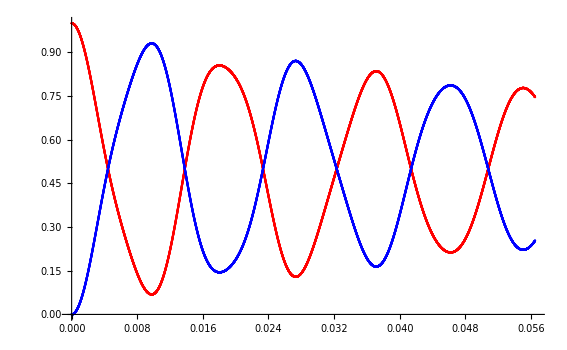

```mathematica
Clear[a1,a2,a3];
Show[
ListPlot[a1 = Re[Table[{t,Tr[matρ[t].projSysExt[1]]},{t,0,timeCm,timestep}]],PlotStyle->Red],
ListPlot[a2 = Re[Table[{t,Tr[matρ[t].projSysExt[2]]},{t,0,timeCm,timestep}]],PlotStyle->Blue],
ListPlot[a3 = Re[Table[{t,Tr[matρ[t].projSysExt[3]]},{t,0,timeCm,timestep}]],PlotStyle->Green],
PlotRange->{{0,timeCm},All}, AxesOrigin->{0,0}
]
```

## Result saving

```mathematica
Export[NotebookDirectory[]<>"resRho11.csv",a1,"CSV"]
Export[NotebookDirectory[]<>"resRho22.csv",a2,"CSV"]
Export[NotebookDirectory[]<>"resRho12.csv",a3,"CSV"]
```

/Users/lorenzoesposito/Desktop/Tesi/repository/test/resRho11.csv

/Users/lorenzoesposito/Desktop/Tesi/repository/test/resRho22.csv

/Users/lorenzoesposito/Desktop/Tesi/repository/test/resRho12.csv

## Occupation number

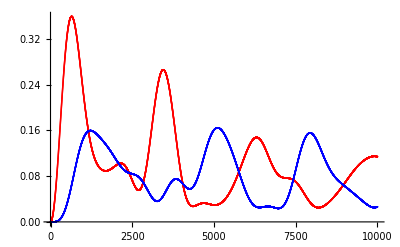

```mathematica
Show[
ListPlot[Table[Tr[matρ[t].aDaga[1].a[1]],{t,0,timeCm,timestep}],PlotStyle->Red],
ListPlot[Table[Tr[matρ[t].aDaga[2].a[2]],{t,0,timeCm,timestep}],PlotStyle->Blue],
PlotRange->All
]
```

```mathematica
Export[NotebookDirectory[]<>"Occupation1.csv",a1,"CSV"]
Export[NotebookDirectory[]<>"Occupation2.csv",a2,"CSV"]
```

/Users/lorenzoesposito/Desktop/Tesi/repository/test/Occupation1.csv

/Users/lorenzoesposito/Desktop/Tesi/repository/test/Occupation2.csv